```mathematica
ClearAll["Global`*"]
```

```mathematica
table1p5nF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C1,5nF_2019_09_02_16_31_52.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable=Delete[table1p5nF, 1];
```

```mathematica
table150pF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C150pF_2019_09_02_16_40_03.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable1=Delete[table150pF, 1];
```

```mathematica
table2p2mkF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C2,2mkF_2019_09_02_16_47_31.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable2=Delete[table2p2mkF, 1];
```

```mathematica
table150plus = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C151+0,001pF_2019_09_03_14_09_48.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable3 = Delete[table150plus, 1];
table0=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\CapacitanceSubstituter0F_2019_09_03_14_26_31.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable0=Delete[table0, 1];
```

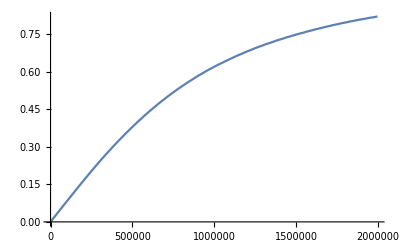

```mathematica
ListLinePlot[table1p5nF]
```

```mathematica
ZparallelRC[R_, C_, ω_] := (R×1/(ⅈ×ω×C))/(R+1/(ⅈ×ω×C))
```

```mathematica
N[ZparallelRC[46.5, 25*10^-12, ω]]
```

-(0.+1.86×10^12 ⅈ)/((46.5-(0.+4.×10^10 ⅈ)/ω) ω)

```mathematica
ZC[ω_, Rp_, C0_, Rs_, Ls_]:=50+ⅈ×ω×Ls+ZparallelRC[Rp, C0, ω]+Rs+ZparallelRC[46.5, 25×10^-12, ω]
```

```mathematica
(*Zreal[ω_,  Rp_, C0_, Rs_] := 50 + Rp/(1+Rp^2*ω^2*C0^2)+  Rs + 46.5/(1+46.5^2*ω^2*(25*10^-12)^2)*)
```

```mathematica
(*Zim[ω_, Ls_, Rp_, C0_]:=ω*Ls-(ω*Rp^2*C0)/(1+Rp^2*ω*C0^2)-(ω*46.5^2*(25*10^-12))/(1+46.5^2*ω*(25*10^-12)^2)*)а
```

а

```mathematica
AbsZ[ω_, Rp_, C0_, Rs_, Ls_]:=√(Zim[2π×ω, Ls, Rp, C0]^2+Zreal[2π×ω,  Rp, C0, Rs]^2)
```

```mathematica
Uin[ω_, Ls_, Rp_, C0_, Rs_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[ZC[2π×ω, Rp, C0, Rs, Ls]]]
```

```mathematica
(*Manipulate[Show[Plot[Uin[ω, Ls, Rp, 1.5*10^-9, Rs],{ω,Min[newtable[[All,1]]],Max[newtable[[All,1]]]}],ListLinePlot[newtable, PlotStyle->Green]], {Ls, 10^-12, 10^-5}, {Rp, 10^5, 10^12}, {Rs, 10^-12, 10^-5}]*)
```

```mathematica
(*Manipulate[Show[Plot[Uin[ω, Ls, Rp, 150*10^-12, Rs],{ω,Min[newtable[[All,1]]],Max[newtable[[All,1]]]}],ListLinePlot[newtable1, PlotStyle->Green]], {Ls, 10^-12, 10^-5}, {Rp, 10^5, 10^12}, {Rs, 10^-12, 10^-5}]*)
```

```mathematica
(*Manipulate[Show[Plot[Uin[ω, Ls, Rp, 2.2*10^-6, Rs],{ω,Min[newtable2[[All,1]]],Max[newtable2[[All,1]]]}],ListLinePlot[newtable2, PlotStyle->Green]], {Ls, 10^-12, 10^-5}, {Rp, 10^4, 10^12}, {Rs, 10^-12, 10^-5}]*)
```

```mathematica
fit1p5= FindFit[newtable, Uin[ω, Ls, Rp, C0, Rs], {{Ls,10^-6}, {Rp,10^5}, {C0,1.5*10^-9}, {Rs, 10^-6}}, ω,MaxIterations->10000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→5.38582×10^-7,Rp→3.27504×10^7,C0→1.41717×10^-9,Rs→5.77458}

```mathematica
fit1p5["ParameterTable"]
```

{Ls→5.38582×10^-7,Rp→3.27504×10^7,C0→1.41717×10^-9,Rs→5.77458}[ParameterTable]

```mathematica
n1p5= NonlinearModelFit[newtable, Uin[ω, Ls, Rp, C0, Rs], {{Ls,10^-6}, {Rp,10^5}, {C0,1.5*10^-9}, {Rs, 10^-6}}, ω,MaxIterations->10000]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[5.92056×10^11 Re[Abs[1/((46.5-(20000000000 ⅈ)/(π ω)) ω)]/Abs[55.7746-(0.+«22» ⅈ)/((«21»-(«1»)/ω) ω)-(0.+«1»)/((«1») ω)+(0.+3.38401×10^-6 ⅈ) ω]]]

```mathematica
n1p5["ParameterTable"]
```

General::munfl: (1.2148×10^-33)^198. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00267785^198. is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
Ls | 5.38582×10^-7 | 1.30909×10^-7 | 4.11416 | 0.0000472907
Rp | 3.27504×10^7 | 5.73616×10^-11 | 5.70946×10^17 | 0.
C0 | 1.41717×10^-9 | 3.6902×10^-12 | 384.036 | 0.
Rs | 5.77458 | 0.836407 | 6.90404 | 2.01924×10^-11

```mathematica
fit150= FindFit[newtable1, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^5}, {C0,150*10^-12}, {Rs, 10^-5}}, ω,MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→9.82663×10^-7,Rp→463089.,C0→1.51697×10^-10,Rs→43.1451}

```mathematica
n150=NonlinearModelFit[newtable1, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^5}, {C0,150*10^-12}, {Rs, 10^-5}}, ω,MaxIterations->1000]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[5.92056×10^11 Re[Abs[1/((46.5-(20000000000 ⅈ)/(π ω)) ω)]/Abs[93.1451-(0.+«22» ⅈ)/((«18»-(«1»)/ω) ω)-(0.+«1»)/((«5»-«1»)«1»«1»)+(0.+6.17425×10^-6 ⅈ) ω]]]

```mathematica
n150["ParameterTable"]
```

General::munfl: (2.82135×10^-18)^398. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0139177^398. is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
Ls | 9.82663×10^-7 | 1.00857×10^-7 | 9.7431 | 2.87856×10^-21
Rp | 463089. | 0.00002757 | 1.67969×10^10 | 0.
C0 | 1.51697×10^-10 | 6.38775×10^-13 | 237.481 | 0.
Rs | 43.1451 | 4.41204 | 9.77894 | 2.09927×10^-21

```mathematica
fit2p2= FindFit[newtable2, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^7}, {C0,2.2*10^-6}, {Rs, 10^-5}}, ω,MaxIterations->10000]
```

{Ls→0.0000859548,Rp→6.82686×10^10,C0→2.12857×10^-6,Rs→2.468}

```mathematica
n2p2=NonlinearModelFit[newtable2, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^7}, {C0,2.2*10^-6}, {Rs, 10^-5}}, ω,MaxIterations->10000]
```

FittedModel[5.92056×10^11 Re[Abs[1/((46.5-(20000000000 ⅈ)/(π ω)) ω)]/Abs[52.468-(0.+«22» ⅈ)/((«23»-(«1»)/ω) ω)-(0.+«1»)/((«1») ω)+(0.+0.00054007 ⅈ) ω]]]

```mathematica
n2p2["ParameterTable"]
```

General::munfl: (1.22874×10^-57)^52.5 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
Ls | 0.0000859548 | 4.74891×10^-6 | 18.0999 | 4.64466×10^-34
Rp | 6.82686×10^10 | 2.33538×10^-19 | 2.92324×10^29 | 0.
C0 | 2.12857×10^-6 | 2.20219×10^-9 | 966.573 | 3.55298×10^-209
Rs | 2.468 | 0.0135472 | 182.178 | 3.79624×10^-133

```mathematica
fit150plus = FindFit[newtable3, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^5}, {C0,150*10^-12}, {Rs, 10^-5}}, ω,MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→9.55773×10^-7,Rp→-84440.2,C0→1.47246×10^-10,Rs→2.83147}

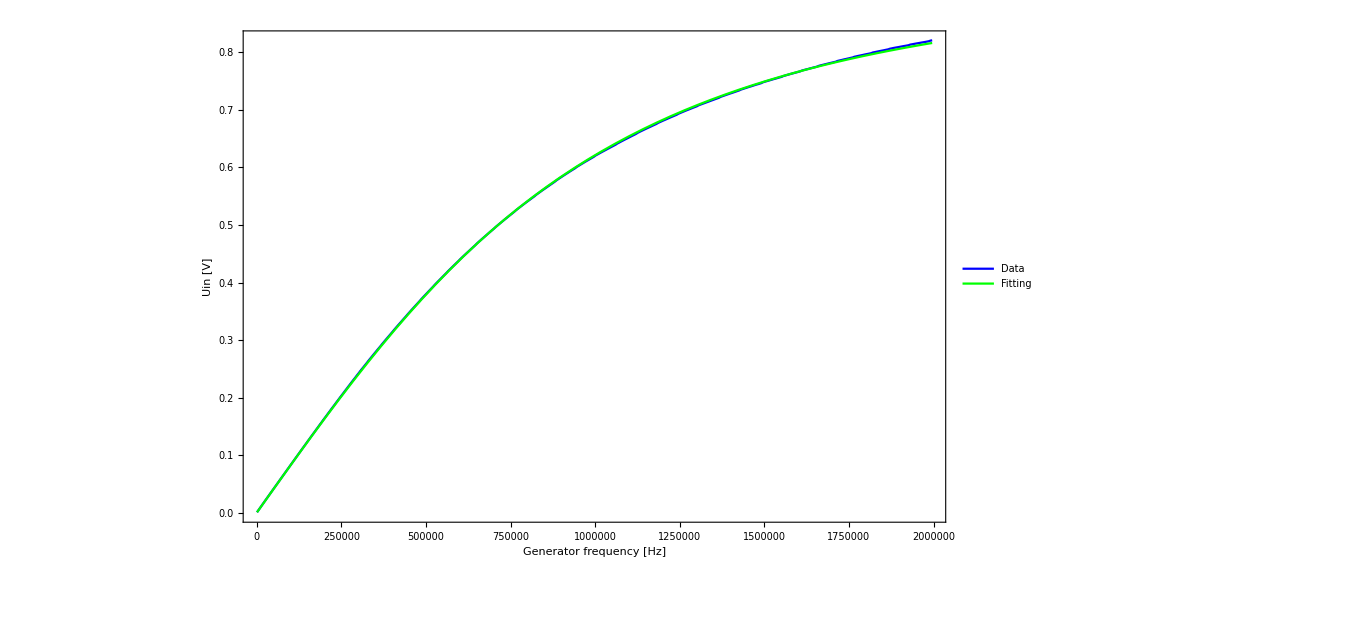

```mathematica
Legended[Show[ListLinePlot[newtable, PlotStyle->Blue],
Plot[Uin[ω,Ls,Rp,C0,Rs]/.fit1p5,{ω,Min[newtable[[All,1]]],Max[newtable[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Uin [V]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

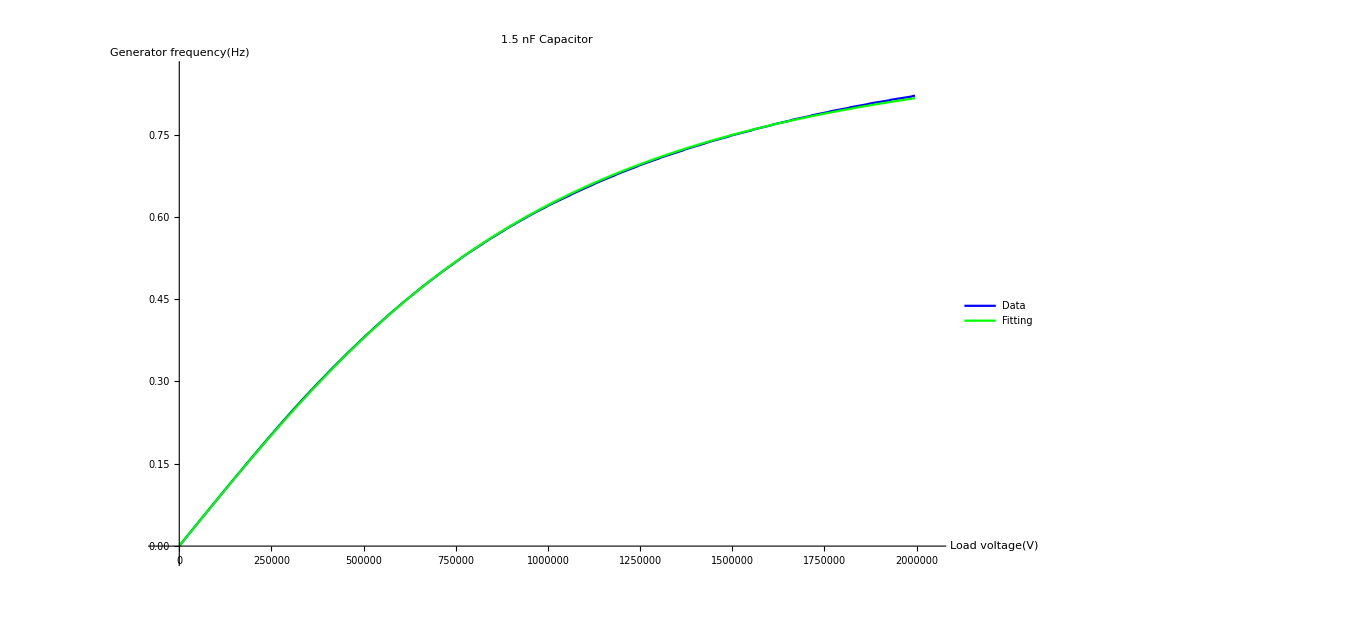

-Graphics-

```mathematica
□_□
```

□_□

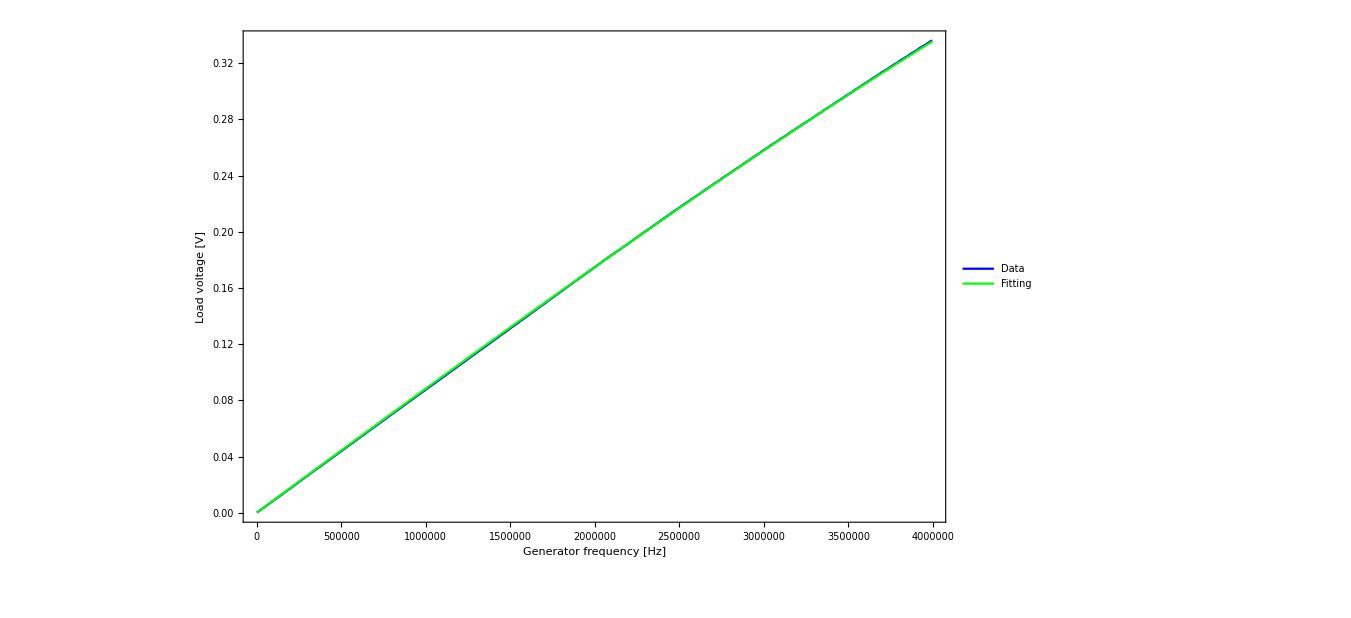

```mathematica
Legended[Show[ListLinePlot[newtable1, PlotStyle->Blue],Plot[Uin[ω,Ls,Rp,C0,Rs]/.fit150,{ω,Min[newtable1[[All,1]]],Max[newtable1[[All,1]]]},PlotStyle->Green],Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

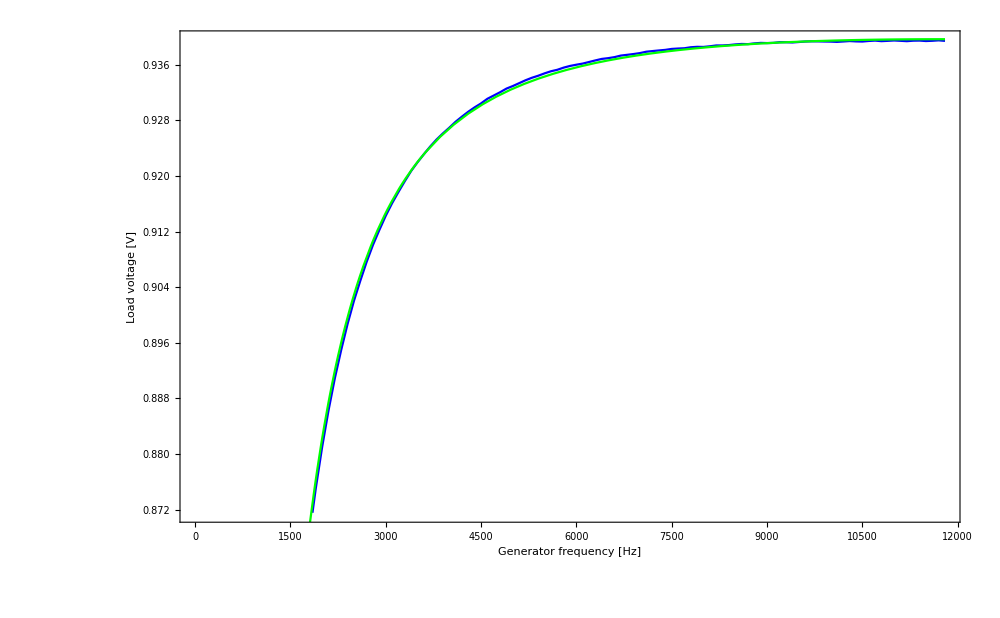

```mathematica
Show[ListLinePlot[newtable2, PlotStyle->Blue],Plot[Uin[ω,Ls,Rp,C0,Rs]/.fit2p2,{ω,Min[newtable2[[All,1]]],Max[newtable2[[All,1]]]},PlotStyle->Green],Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->24}]
```

```mathematica
(*nlm=NonlinearModelFit[newtable, Uin[ω, Ls, Rp, C0, Rs], {Ls, Rp, {C0,1.5*10^-9}, Rs}, ω,MaxIterations->10000]*)
```

```mathematica
(*nlm["ParameterTable"]*)
```

```mathematica
table114pF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\CapacitanceSubstituter114pF_2019_09_03_14_43_04.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable114 = Delete[table114pF, 1];
f1[a_,x_]:=a*x
```

```mathematica
table113pF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\CapacitanceSubstituter113pF_2019_09_03_14_46_35.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable113 = Delete[table113pF, 1];
```

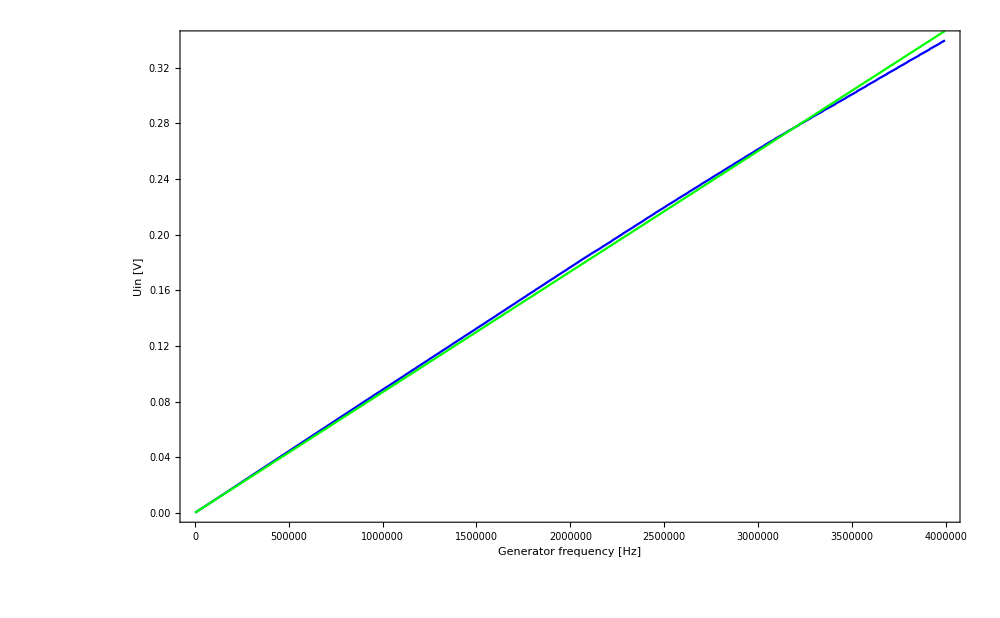

```mathematica
Show[ListLinePlot[newtable3, PlotStyle->Blue],Plot[f1[8.67*10^-8,x],{x,Min[newtable3[[All,1]]],Max[newtable3[[All,1]]]},PlotStyle->Green],Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Uin [V]"},ImageSize->1000, BaseStyle->{FontSize->24}]
```

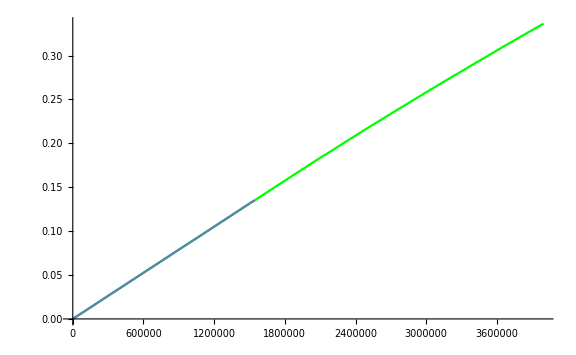

```mathematica
Show[ListLinePlot[newtable1, PlotStyle->Green], ListLinePlot[newtable114], ImageSize->Large]
```

```mathematica
fit150= FindFit[newtable114, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^5}, {C0,150*10^-12}, {Rs, 10^-5}}, ω,MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→9.581×10^-7,Rp→260969.,C0→1.49703×10^-10,Rs→2.46758}

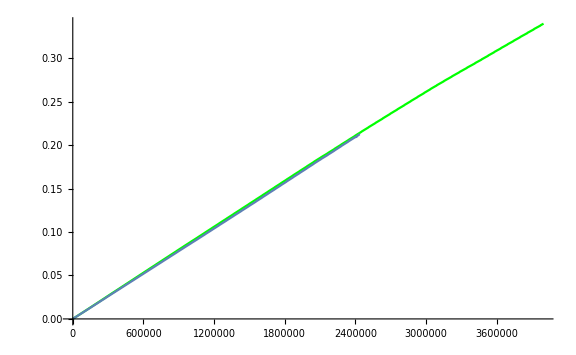

```mathematica
Show[ListLinePlot[newtable3, PlotStyle->Green], ListLinePlot[newtable113], ImageSize->Large]
```

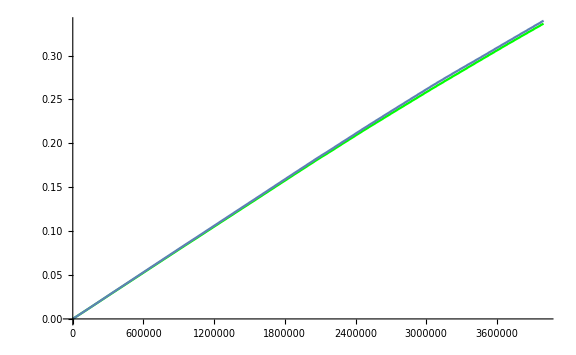

```mathematica
Show[ListLinePlot[newtable1, PlotStyle->Green], ListLinePlot[newtable3], ImageSize->Large]
```

```mathematica
fitLinear150 = FindFit[newtable1, a×ω,{a},ω]
```

{a→8.5837906884725513749×10^-8}

```mathematica
fitLinear150plus= FindFit[newtable3, a×ω,{a},ω]
```

{a→8.6740319766596553061×10^-8}

```mathematica
fitLinear114= FindFit[newtable114, a×ω,{a},ω]
```

{a→8.7566074281124882709×10^-8}

```mathematica
fitLinear113= FindFit[newtable113, a×ω,{a},ω]
```

{a→8.7045905853758675236×10^-8}

```mathematica
fitLinear0= FindFit[newtable0, a×ω,{a},ω]
```

{a→2.252218323869018495×10^-8}

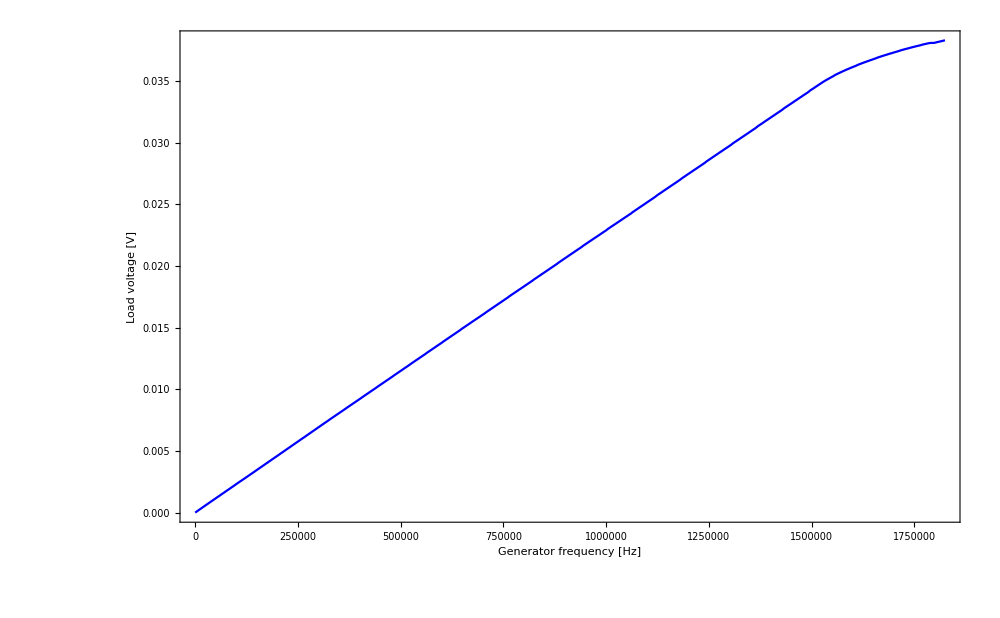

```mathematica
Show[ListLinePlot[newtable0, PlotStyle->Blue],Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->24}]
```